# J20 Integral

### Parameters

```mathematica
(* a = 2 *)pbarRoot = {0.196944,0.529488,1.01027,1.64062,2.42201,3.35626,4.44557,5.69258,7.10035,8.67249,10.4131,12.3271,14.4199,16.6978,19.1681,21.8392,24.7207,27.824,31.1622,34.7509,38.6084,42.7572,47.2244,52.0436,57.2578,62.9227,69.1137,75.9368,83.5518,92.2213,102.448,115.525};

pbarWeight={0.00825034,0.0671033,0.206386,0.368179,0.44639,0.397211,0.270703,0.144937,0.0619302,0.0213228,0.00594841,0.00134795,0.000248167,3.70532*10^-05,4.47058*10^-06,4.33555*10^-07,3.35571*10^-08,2.05432*10^-09,9.83647*10^-11,3.63364*10^-12,1.01835*10^-13,2.1211*10^-15,3.201*10^-17,3.39007*10^-19,2.41905*10^-21,1.10271*10^-23,2.98827*10^-26,4.34972*10^-29,2.92108*10^-32,7.05339*10^-36,3.81617*10^-40,1.39865*10^-45};

GeVinversefm = 5.067731;

μBpts = 100;
Tpts = 100;

μBmin = 0.0;
μBmax = 4.06;
dμB=(μBmax-μBmin)/μBpts;
μBgrid=Table[μBmin+(i-1)*dμB,{i,1,μBpts+1}];

Tmin = 0.1;
Tmax = 0.82;
dT=(Tmax-Tmin)/Tpts;
Tgrid=Table[Tmin+(i-1)*dT,{i,1,Tpts+1}];
```

## Meson

### Proton

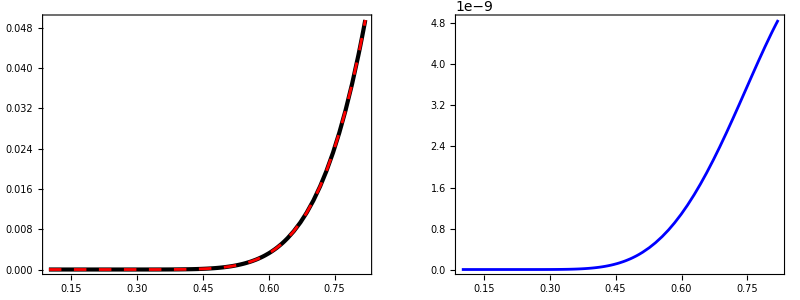

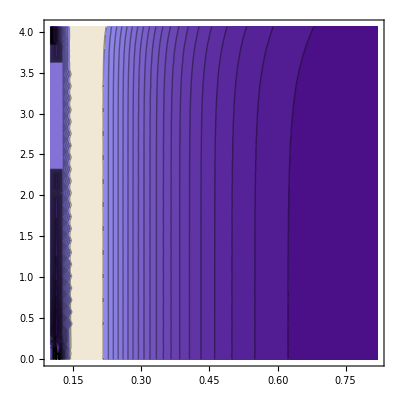

```mathematica
m = 0.938*GeVinversefm;
dof = 2.0;
θ=1.0;
M20Integrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
M20GaussIntegrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*((pbar)^2+(m/T)^2)^(1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T] +θ)^2));
M20=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[M20Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*M20GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20=Interpolation[M20];
M20Gauss=Interpolation[M20Gauss];
GraphicsGrid[{{Plot[{M20[T,0.0],M20Gauss[T,0.0]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[M20[T,0.0]-M20Gauss[T,0.0]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(M20[T,μB]-M20Gauss[T,μB])/M20[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(M20[T,μB]-M20Gauss[T,μB])/M20[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Lambda

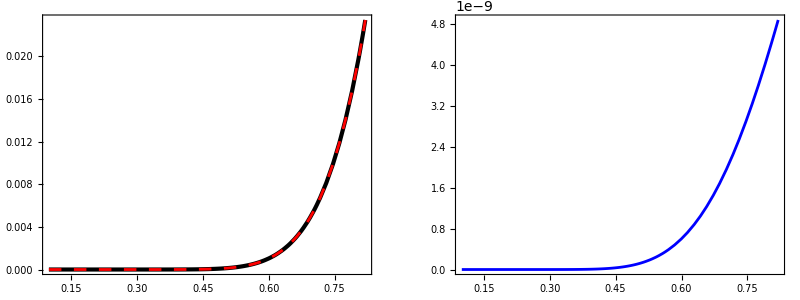

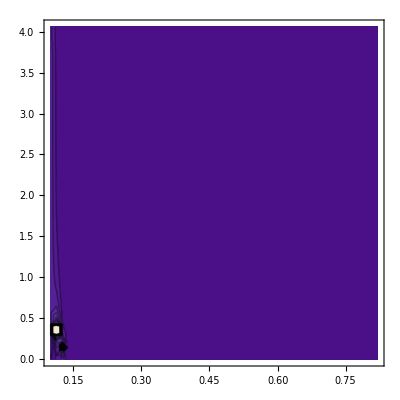

```mathematica
m = 1.11568*GeVinversefm;
dof = 2.0;
θ=1.0;
M20Integrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
M20GaussIntegrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*((pbar)^2+(m/T)^2)^(1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T] +θ)^2));
M20=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[M20Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*M20GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20=Interpolation[M20];
M20Gauss=Interpolation[M20Gauss];

GraphicsGrid[{{Plot[{M20[T,0.0],M20Gauss[T,0.0]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[M20[T,0.0]-M20Gauss[T,0.0]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(M20[T,μB]-M20Gauss[T,μB])/M20[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(M20[T,μB]-M20Gauss[T,μB])/M20[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega

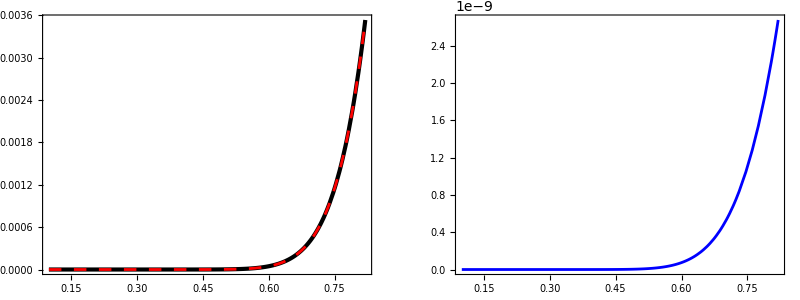

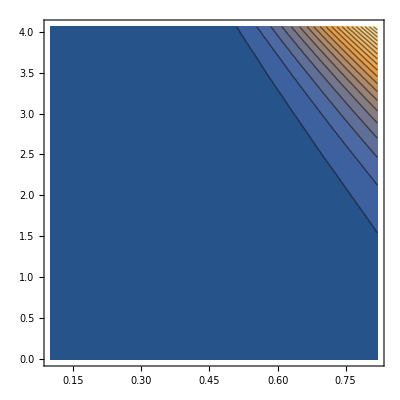

```mathematica
m = 1.67243*GeVinversefm;
dof = 4.0;
θ=1.0;
M20Integrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
M20GaussIntegrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*((pbar)^2+(m/T)^2)^(1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T] +θ)^2));
M20=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[M20Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*M20GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20=Interpolation[M20];
M20Gauss=Interpolation[M20Gauss];

GraphicsGrid[{{Plot[{M20[T,0.0],M20Gauss[T,0.0]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[M20[T,0.0]-M20Gauss[T,0.0]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]

GraphicsGrid[{{Plot3D[{M20[T,μB],M20Gauss[T,μB]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[M20[T,μB]-M20Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega2250

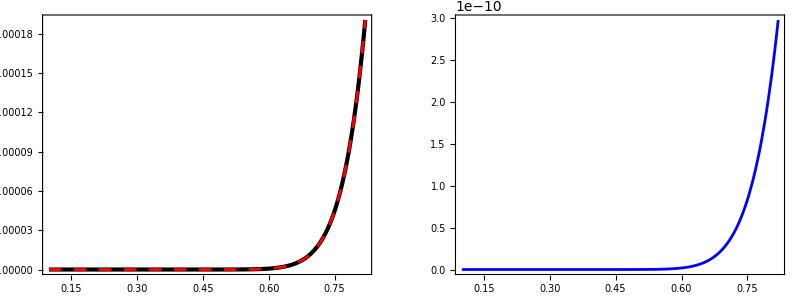

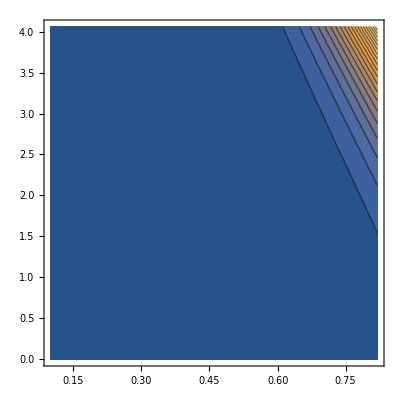

```mathematica
m = 2.25200*GeVinversefm;
dof = 4.0;
θ=1.0;
M20Integrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
M20GaussIntegrand[T_,μB_,pbar_]:=(dof*T^4)/(2.0*Pi^2)*((pbar)^2+(m/T)^2)^(1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T] +θ)^2));
M20=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[M20Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*M20GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
M20=Interpolation[M20];
M20Gauss=Interpolation[M20Gauss];

GraphicsGrid[{{Plot[{M20[T,0.0],M20Gauss[T,0.0]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[M20[T,0.0]-M20Gauss[T,0.0]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]

GraphicsGrid[{{Plot3D[{M20[T,μB],M20Gauss[T,μB]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[M20[T,μB]-M20Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```